```mathematica
f[x_,θ1_,θ2_,q1_,q2_,s1_:1,s2_:1]:= ⅇ^(-s1 (x-q1) (θ1-If[x<q1,1,0])-s2 (x-q2) (θ2-If[x<q2,1,0]))
```

```mathematica
f[y,Subscript[θ, 1],Subscript[θ, 2],Subscript[q, 1],Subscript[q, 2]]
```

ⅇ^((-y+q_1) (-If[y<q_1,1,0]+θ_1)-(y-q_2) (-If[y<q_2,1,0]+θ_2))

```mathematica
E1= Integrate[  f[x,Subscript[θ, 1],Subscript[θ, 2],Subscript[q, 1],Subscript[q, 2]],{x,-∞,∞} ,Assumptions->Subscript[θ, 1]<1&& Subscript[θ, 1]>0&&Subscript[θ, 2]<1&& Subscript[θ, 2]>0&&Subscript[q, 1]>Subscript[q, 2]&&Subscript[θ, 1]>Subscript[θ, 2]]
```

-(-2 ⅇ^((-q_1+q_2) θ_2)+ⅇ^((q_1-q_2) (-1+θ_1)) θ_1+ⅇ^((-q_1+q_2) θ_2) θ_1+ⅇ^((q_1-q_2) (-1+θ_1)) θ_2+ⅇ^((-q_1+q_2) θ_2) θ_2)/((-2+θ_1+θ_2) (-1+θ_1+θ_2) (θ_1+θ_2))

```mathematica
Simplify[-(x-q1) (θ1-If[x<q1,1,0])-(x-q2) (θ2-If[x<q2,1,0]),Assumptions->q1>q2 && x>q1&&θ1>θ2]
```

q1 θ1+q2 θ2-x (θ1+θ2)

```mathematica
M1 = Integrate[  x/E1 f[x,Subscript[θ, 1],Subscript[θ, 2],Subscript[q, 1],Subscript[q, 2]] ,{x,-∞,∞} ,Assumptions->Subscript[θ, 1]<1&& Subscript[θ, 1]>0&&Subscript[θ, 2]<1&& Subscript[θ, 2]>0&&Subscript[q, 1]>Subscript[q, 2]&&Subscript[θ, 1]>Subscript[θ, 2]]
```

(-4 ⅇ^((-q_1+q_2) θ_2)+12 ⅇ^((-q_1+q_2) θ_2) θ_1-4 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1-3 ⅇ^((q_1-q_2) (-1+θ_1)) θ_1^2-9 ⅇ^((-q_1+q_2) θ_2) θ_1^2+8 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1^2+2 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1^2+2 ⅇ^((q_1-q_2) (-1+θ_1)) θ_1^3+2 ⅇ^((-q_1+q_2) θ_2) θ_1^3-5 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1^3-3 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1^3+ⅇ^((-q_1+q_2) θ_2) q_1 θ_1^4+ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1^4+12 ⅇ^((-q_1+q_2) θ_2) θ_2-4 ⅇ^((-q_1+q_2) θ_2) q_1 θ_2-6 ⅇ^((q_1-q_2) (-1+θ_1)) θ_1 θ_2-18 ⅇ^((-q_1+q_2) θ_2) θ_1 θ_2+16 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1 θ_2+4 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1 θ_2+6 ⅇ^((q_1-q_2) (-1+θ_1)) θ_1^2 θ_2+6 ⅇ^((-q_1+q_2) θ_2) θ_1^2 θ_2-15 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1^2 θ_2-9 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1^2 θ_2+4 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1^3 θ_2+4 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1^3 θ_2-3 ⅇ^((q_1-q_2) (-1+θ_1)) θ_2^2-9 ⅇ^((-q_1+q_2) θ_2) θ_2^2+8 ⅇ^((-q_1+q_2) θ_2) q_1 θ_2^2+2 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_2^2+6 ⅇ^((q_1-q_2) (-1+θ_1)) θ_1 θ_2^2+6 ⅇ^((-q_1+q_2) θ_2) θ_1 θ_2^2-15 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1 θ_2^2-9 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1 θ_2^2+6 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1^2 θ_2^2+6 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1^2 θ_2^2+2 ⅇ^((q_1-q_2) (-1+θ_1)) θ_2^3+2 ⅇ^((-q_1+q_2) θ_2) θ_2^3-5 ⅇ^((-q_1+q_2) θ_2) q_1 θ_2^3-3 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_2^3+4 ⅇ^((-q_1+q_2) θ_2) q_1 θ_1 θ_2^3+4 ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_1 θ_2^3+ⅇ^((-q_1+q_2) θ_2) q_1 θ_2^4+ⅇ^((q_1-q_2) (-1+θ_1)) q_2 θ_2^4)/((-2+θ_1+θ_2) (-1+θ_1+θ_2) (θ_1+θ_2) (-2 ⅇ^((-q_1+q_2) θ_2)+ⅇ^((q_1-q_2) (-1+θ_1)) θ_1+ⅇ^((-q_1+q_2) θ_2) θ_1+ⅇ^((q_1-q_2) (-1+θ_1)) θ_2+ⅇ^((-q_1+q_2) θ_2) θ_2))

```mathematica
f[2.1,0.2,0.5,1,2]
```

0.763379

```mathematica
SE1= Integrate[  f[x,0.01,0.3,1,5,3,0.5],{x,-∞,∞}]
```

7.00262

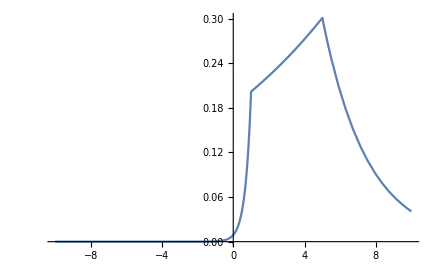

```mathematica
Plot[f[x,0.1,0.2,1,5,3,0.5]/1,{x,-10,10},PlotRange->Full]
```

```mathematica
Collect[Simplify[-(x-q1) (p1-If[x<=q1,1,0])/s1+(x-q2) (p2-If[x<=q2,1,0])/s2,Assumptions->q2>q1 && x<=q1],x]
```

(q2 (s1-p2 s1)+(-1+p1) q1 s2)/(s1 s2)+(((-1+p2) s1+s2-p1 s2) x)/(s1 s2)

```mathematica
Collect[Simplify[-(x-q1) (p1-If[x<=q1,1,0])/s1+(x-q2) (p2-If[x<=q2,1,0])/s2,Assumptions->q2>q1 && x<=q2&& x>q1],x]
```

(q2 (s1-p2 s1)+p1 q1 s2)/(s1 s2)+(((-1+p2) s1-p1 s2) x)/(s1 s2)

```mathematica
Collect[Simplify[-(x-q1) (p1-If[x<=q1,1,0])/s1+(x-q2) (p2-If[x<=q2,1,0])/s2,Assumptions->q2>q1  x>q2],x]
```

(q2 (s1-p2 s1)+(-1+p1) q1 s2)/(s1 s2)+(((-1+p2) s1+s2-p1 s2) x)/(s1 s2)

## Medium vs Mean

```mathematica
Collect[Simplify[-(x-q1) (0.5-If[x<=q1,1,0])+(x-q2)^2 /s2,Assumptions->q2>q1 && x>q2],x]
```

(0.+q2^2+0.5 q1 s2)/s2+((-2. q2-0.5 s2) x)/s2+x^2/s2

```mathematica
Simplify[(-2  q2+0.5)^2-4(q2^2-0.5 q1)<0,Assumptions->q2>q1 ]
```

0.125+1. q1<1. q2

```mathematica
Simplify[(2  q2-1)^2-4(q2^2- q1)>0,Assumptions->q2>q1 ]
```

1+4 q1>4 q2

```mathematica
Simplify[(2  q2+1)^2-4(q2^2+ q1)>0,Assumptions->q2>q1 ]
```

True

## Rigid, θ1<θ2, q11<q21

```mathematica
g[x_,θ1_,θ2_,q11_,q12_,q21_,q22_]:= (x-q11) (θ1-If[x<=q11,1,0])+(x-q12) (θ2-If[x<=q12,1,0])-(x-q21) (θ1-If[x<=q21,1,0])-(x-q22) (θ2-If[x<=q22,1,0])
```

### case 1: q11<q12<q21<q22

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q12<q21<q22 && x<=q11],{q11,q12,q21,q22}]
```

q11 (1-θ1)+q21 (-1+θ1)+q12 (1-θ2)+q22 (-1+θ2)

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q12<q21<q22 && q11<x<=q12],x]
```

q12-q22+x+q21 (-1+θ1)-q11 θ1-q12 θ2+q22 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q12<q21<q22 && q12<x<=q21],x]
```

2 x+q21 (-1+θ1)-q11 θ1+q22 (-1+θ2)-q12 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q12<q21<q22 && q21<x<=q22],x]
```

x-q11 θ1+q21 θ1+q22 (-1+θ2)-q12 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q12<q21<q22 && x>q22],x]
```

-q11 θ1+q21 θ1+(-q12+q22) θ2

```mathematica
Roots[q12-q22+x+q21 (-1+θ1)-q11 θ1-q12 θ2+q22 θ2==0,x]
```

x==-q12+q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2

```mathematica
Roots[2 x+q21 (-1+θ1)-q11 θ1+q22 (-1+θ2)-q12 θ2==0,x]
```

x==1/2 (q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2)

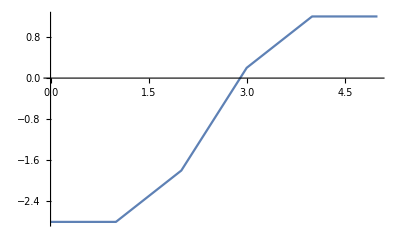

```mathematica
Plot[g[x,0.2,0.4,1,2,3,4],{x,0,5}]
```

### case 2: q11<q21<q12<q22

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q12<q22 && x<=q11],x]
```

q11+q12-q21-q22-q11 θ1+q21 θ1-q12 θ2+q22 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q12<q22 && q11<x<=q21],x]
```

q12-q22+x+q21 (-1+θ1)-q11 θ1-q12 θ2+q22 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q12<q22&& q21<x<=q12],x]
```

q12+(-q11+q21) θ1+q22 (-1+θ2)-q12 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q12<q22 && q12<x<=q22],x]
```

x-q11 θ1+q21 θ1+q22 (-1+θ2)-q12 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q12<q22 && x>q22],x]
```

-q11 θ1+q21 θ1+(-q12+q22) θ2

```mathematica
Roots[q12-q22+x+q21 (-1+θ1)-q11 θ1-q12 θ2+q22 θ2==0,x]
```

x==-q12+q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2

```mathematica
Roots[x-q11 θ1+q21 θ1+q22 (-1+θ2)-q12 θ2==0,x]
```

x==q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2

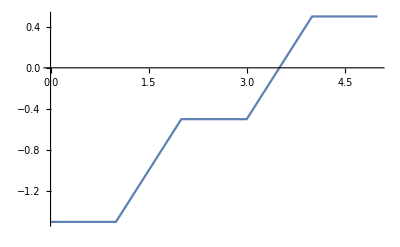

```mathematica
Plot[g[x,0.2,0.3,1,3,2,4],{x,0,5}]
```

### case 3: q11<q21<q22<q12

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q22<q12 && x<=q11],x]
```

q11+q12-q21-q22-q11 θ1+q21 θ1-q12 θ2+q22 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q22<q12 && q11<x<=q21],x]
```

q12-q22+x+q21 (-1+θ1)-q11 θ1-q12 θ2+q22 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q22<q12&& q21<x<=q22],x]
```

q12+(-q11+q21) θ1+q22 (-1+θ2)-q12 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q22<q12&& q22<x<=q12],x]
```

q12-x-q11 θ1+q21 θ1-q12 θ2+q22 θ2

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q22<q12&& x>q12],x]
```

-q11 θ1+q21 θ1+(-q12+q22) θ2

```mathematica
Roots[q12-q22+x+q21 (-1+θ1)-q11 θ1-q12 θ2+q22 θ2==0,x]
```

x==-q12+q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2

```mathematica
Roots[x-q11 θ1+q21 θ1+q22 (-1+θ2)-q12 θ2==0,x]
```

x==q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2

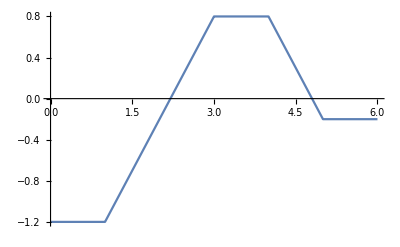

```mathematica
Plot[g[x,0.2,0.6,1,5,3,4],{x,0,6}]
```

```mathematica
Roots[q12-x-q11 θ1+q21 θ1-q12 θ2+q22 θ2==0,x]
```

x==q12-q11 θ1+q21 θ1-q12 θ2+q22 θ2

```mathematica
Integrate[(p(1-p))/σ ⅇ^(-(y-μ)/σ (p-If[(y-μ)/σ<0,1,0])),{y,-∞,+∞},Assumptions-> σ>0 && 0<p<1 ]
```

1

```mathematica
Integrate[y (p(1-p))/σ ⅇ^(-(y-μ)/σ (p-If[(y-μ)/σ<0,1,0])),{y,-∞,+∞},Assumptions-> σ>0 && 0<p<1 ] (* mean *)
```

(-p μ+p^2 μ-σ+2 p σ)/((-1+p) p)

```mathematica
Simplify[Integrate[y^2(p(1-p))/σ ⅇ^(-(y-μ)/σ (p-If[(y-μ)/σ<0,1,0])),{y,-∞,+∞},Assumptions-> σ>0 && 0<p<1 ]]
```

(p^4 μ^2-2 p^3 μ (μ-2 σ)+2 p (μ-3 σ) σ+2 σ^2+p^2 (μ^2-6 μ σ+6 σ^2))/((-1+p)^2 p^2)

```mathematica
Simplify[Integrate[(y^2-y)(p(1-p))/σ ⅇ^(-(y-μ)/σ (p-If[(y-μ)/σ<0,1,0])),{y,-∞,+∞},Assumptions-> σ>0 && 0<p<1 ]](* variance *)
```

(p^4 (-1+μ) μ+2 σ^2-p σ (1-2 μ+6 σ)-2 p^3 (μ^2+σ-μ (1+2 σ))+p^2 (μ^2+3 σ (1+2 σ)-μ (1+6 σ)))/((-1+p)^2 p^2)

```mathematica
(-p μ+p^2 μ-σ+2 p σ)/((-1+p) p)/.{μ->0,p->0.4,σ->0.4}
```

0.333333

```mathematica
(p^4 (-1+μ) μ+2 σ^2-p σ (1-2 μ+6 σ)-2 p^3 (μ^2+σ-μ (1+2 σ))+p^2 (μ^2+3 σ (1+2 σ)-μ (1+6 σ)))/((-1+p)^2 p^2) /.{μ->0,p->0.4,σ->0.7}
```

4.18056

```mathematica
c^(-1+x)
```

c^(-1+x)

```mathematica
D[c^(-1+x), x]
```

c^(-1+x) Log[c]